```mathematica
rnew[x_,y_]= Sqrt[x^2+y^2];
```

```mathematica
λ = 0.800; (*microns*)
γ = π*0.23/180; (*rad*)
γ05 = π*0.5/180; (*rad*)
γ10 = π*1.0/180; (*rad*)
m = 5; (*bessel order*)
k = 2*π/λ; (*microns^-1*)
rp[x_] = k*Sin[x]; (*microns^-1*)
ein = 500*10^-3; (*J*)
tin = 100*10^-15; (*s*)
din = 4.0; (*cm*)
ain =π*(din/2)^2; (*cm^2*)
Pin = ein/(tin*ain); (*W/cm^2*)
zmax[x_] = din/(2*Tan[x]); (*cm*)
r2[x_] = 3.0542/rp[x] ;(*microns*)
r3[x_] = 4.2012/rp[x];(*microns*)
r4[x_] = 5.3175/rp[x]; (*microns*)
r5[x_] = 6.4156/rp[x];
r6[x_] = 7.5013/rp[x];
r7[x_] = 8.5778/rp[x];
r8[x_] = 9.6474/rp[x];
r9[x_] = 10.7114/rp[x];
r10[x_] = 11.7709/rp[x];
rp[γ]
```

0.0315278

```mathematica
Plot[{r3[π*x/180],r4[π*x/180],r5[π*x/180]},{x,0.1,0.5},AxesLabel->{"γ (deg)","r (μm)"},AxesOrigin->{0,0},PlotLegend->{"J_3","J_4","J_5"},PlotLabel->"Channel Radii vs. Convergence Angle"]
```

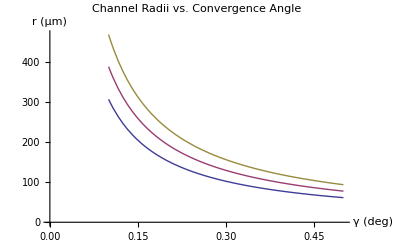

```mathematica
deg300 = 0.312;
γ300 = π*deg300/180; (*rad*)
r5[γ300]
deg400 = 0.234;
γ400 = π*deg400/180; (*rad*)
r5[γ400]
deg500 = 0.187;
γ500 = π*deg500/180; (*rad*)
r5[γ500]
deg600 = 0.156;
γ600 = π*deg600/180; (*rad*)
r5[γ600]
```

150.009

200.012

250.282

300.017

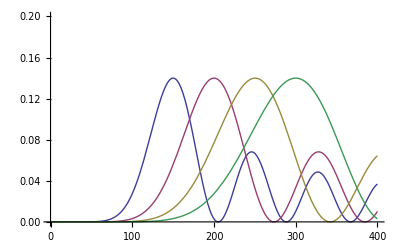

```mathematica
Plot[{BesselJ[5,k*Sin[γ300]*r]^2,BesselJ[5,k*Sin[γ400]*r]^2, BesselJ[5,k*Sin[γ500]*r]^2, BesselJ[5,k*Sin[γ600]*r]^2},{r,0,400},PlotRange->{0,0.2}]
```

```mathematica
deg300 = 0.258;
γ300 = π*deg300/180; (*rad*)
r4[γ300]
deg400 = 0.194;
γ400 = π*deg400/180; (*rad*)
r4[γ400]
deg500 = 0.155;
γ500 = π*deg500/180; (*rad*)
r4[γ500]
deg600 = 0.129;
γ600 = π*deg600/180; (*rad*)
r4[γ600]
```

150.356

199.958

250.27

300.712

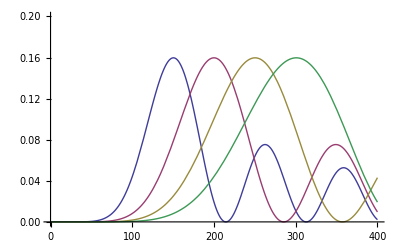

```mathematica
Plot[{BesselJ[4,k*Sin[γ300]*r]^2,BesselJ[4,k*Sin[γ400]*r]^2, BesselJ[4,k*Sin[γ500]*r]^2, BesselJ[4,k*Sin[γ600]*r]^2},{r,0,400},PlotRange->{0,0.2}]
```

```mathematica
deg300 = 0.365;
γ300 = π*deg300/180; (*rad*)
r6[γ300]
deg400 = 0.273;
γ400 = π*deg400/180; (*rad*)
r6[γ400]
deg500 = 0.219;
γ500 = π*deg500/180; (*rad*)
r6[γ500]
deg600 = 0.182;
γ600 = π*deg600/180; (*rad*)
r6[γ600]
```

149.927

200.451

249.877

300.676

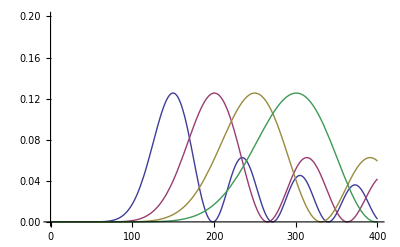

```mathematica
Plot[{BesselJ[6,k*Sin[γ300]*r]^2,BesselJ[6,k*Sin[γ400]*r]^2, BesselJ[6,k*Sin[γ500]*r]^2, BesselJ[6,k*Sin[γ600]*r]^2},{r,0,400},PlotRange->{0,0.2}]
```

```mathematica
deg300 = 0.415;
γ300 = π*deg300/180; (*rad*)
r7[γ300]
deg400 = 0.312;
γ400 = π*deg400/180; (*rad*)
r7[γ400]
deg500 = 0.250;
γ500 = π*deg500/180; (*rad*)
r7[γ500]
deg600 = 0.208;
γ600 = π*deg600/180; (*rad*)
r7[γ600]
```

150.787

200.565

250.305

300.847

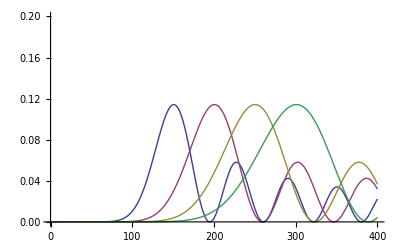

```mathematica
Plot[{BesselJ[7,k*Sin[γ300]*r]^2,BesselJ[7,k*Sin[γ400]*r]^2, BesselJ[7,k*Sin[γ500]*r]^2, BesselJ[7,k*Sin[γ600]*r]^2},{r,0,400},PlotRange->{0,0.2}]
```

```mathematica
deg300 =  0.312;
γ300 = π*deg300/180; (*rad*)
r5[γ300]
deg400 = 0.273;
γ400 = π*deg400/180; (*rad*)
r6[γ400]
deg500 = 0.250;
γ500 = π*deg500/180; (*rad*)
r7[γ500]
deg600 = 0.235;
γ600 = π*deg600/180; (*rad*)
r8[γ600]
```

150.009

200.451

250.305

299.486

```mathematica
Rasterize[Plot[{BesselJ[5,k*Sin[γ300]*r]^2,BesselJ[6,k*Sin[γ400]*r]^2, BesselJ[7,k*Sin[γ500]*r]^2, BesselJ[8,k*Sin[γ600]*r]^2},{r,0,400},PlotRange->{0,0.2},AxesLabel->{"r (μm)","Intensity (arb)"},PlotLegends->{"J_5, γ = 0.312^o, D = 300 μm","J_6, γ = 0.273^o, D = 400 μm","J_7, γ = 0.250^o, D = 500 μm","J_8, γ = 0.235^o, D = 600 μm"},PlotLabel->"Bessel Profiles"]]
```

-Graphics-

```mathematica
Rasterize[Plot[{BesselJ[4,k*Sin[γ10]*r]^2,BesselJ[5,k*Sin[γ10]*r]^2, BesselJ[4,k*Sin[γ05]*r]^2, BesselJ[5,k*Sin[γ05]*r]^2},{r,0,400},PlotRange->{0,0.2},AxesLabel->{"r (μm)","Intensity (arb)"},PlotLegends->{"J_4, γ = 1.0^o, D = 78 μm","J_5, γ = 1.0^o, D = 94 μm","J_4, γ = 0.5^o, D = 155 μm","J_5, γ = 0.5^o, D = 187 μm"},PlotLabel->"Bessel Profiles"]]
```

-Graphics-

```mathematica
deg300 =  0.415;
γ300 = π*deg300/180; (*rad*)
r7[γ300]
deg400 = 0.352;
γ400 = π*deg400/180; (*rad*)
r8[γ400]
deg500 = 0.312;
γ500 = π*deg500/180; (*rad*)
r9[γ500]
deg600 = 0.235;
γ600 = π*deg600/180; (*rad*)
r10[γ600]
```

150.787

199.942

250.453

365.406

```mathematica
Subscript[c, α][x_] = π*Sin[x]^2 * (1+Cos[x])^2/(2*Cos[x]);
P5[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[5,k*Sin[γ05]*r]^2;
P4[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[4,k*Sin[γ05]*r]^2;
P3[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[3,k*Sin[γ05]*r]^2;
P2[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[2,k*Sin[γ05]*r]^2;
P0[r_,z_] = Pin*Subscript[c, α][γ05]*k*1000*z*BesselJ[0,k*Sin[γ05]*r]^2;
P52[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[5,k*Sin[γ10]*r]^2;
P42[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[4,k*Sin[γ10]*r]^2;
P32[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[3,k*Sin[γ10]*r]^2;
P22[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[2,k*Sin[γ10]*r]^2;
P02[r_,z_] = Pin*Subscript[c, α][γ10]*k*1000*z*BesselJ[0,k*Sin[γ10]*r]^2;
```

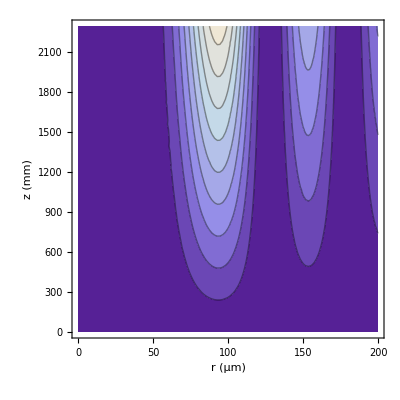

```mathematica
ContourPlot[P5[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

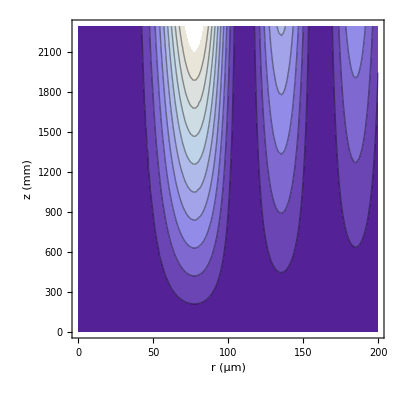

```mathematica
ContourPlot[P4[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

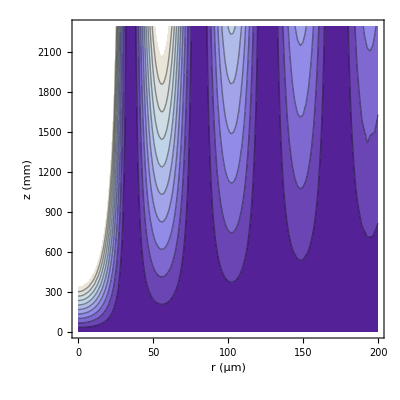

```mathematica
ContourPlot[P0[r,z],{r,0,200},{z,0,zmax[γ]*10},AxesLabel->{"r (μm)","z (mm)"},PlotRange->{0,5*10^14}]
```

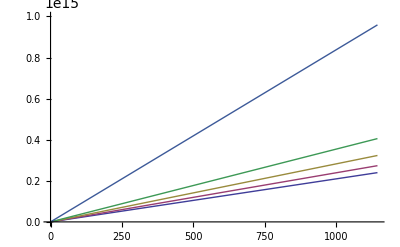

```mathematica
Plot[{P5[r5[γ05],z],P4[r4[γ05],z],P3[r3[γ05],z],P2[r2[γ05],z],P52[r5[γ10],z],P42[r4[γ10],z],P32[r3[γ10],z],P22[r2[γ10],z]},{z,0,zmax[γ]*10}]
```

```mathematica
P42[r4[γ10],900]
```

8.597×10^14

```mathematica
NSolve[P[r5[γ],z]==1.5*10^14,z]
zmax[γ]*10
```

{{z→2439.88}}

2291.77

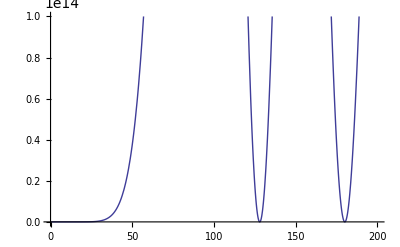

```mathematica
Plot[P[r,zmax[γ]*10],{r,0,200},PlotRange->{0,1*10^14}]
```

```mathematica
ContourPlot[Pin*Subscript[c, α][γ]*k*1000*500*BesselJ[5,rnew[k*Sin[γ]*x,k*Sin[γ]*y]]^2,{x,-200,200},{y,-200,200},PlotRange->{0,1*10^14},PlotPoints->50,ColorFunction->"BlueGreenYellow",AxesLabel->{"x (μm)","y (μm)"}]
```

```mathematica
ContourPlot[Pin*Subscript[c, α][γ]*k*1000*500*BesselJ[0,rnew[k*Sin[γ]*x,k*Sin[γ]*y]]^2,{x,-200,200},{y,-200,200},PlotRange->{0,1*10^14},PlotPoints->50,ColorFunction->"BlueGreenYellow",AxesLabel->{"x (μm)","y (μm)"}]
```

-Graphics-